## List of elastic maps to choose from (first run common_funs.nb) The lattice diagrams are generated in ES_FindSymGroups_output.nb tpert[] is for how much you can add to t = 1 before the Tmat(t) becomes unstable (>=1 negative eigenvalue) contours[] and MaxForScaling[] commands are for setting the color legend on the ball plots.

## Functions and choices

```mathematica
Clear[contours,MaxForScaling]
```

#### function to display Tmat (BB basis) and corresponding Cmat (Voigt)

```mathematica
PrintVoigt[TmatInput_]:=(
Print["The [T]_𝔹𝔹 matrix is ",MatrixForm[Chop[TmatInput,0.0001]]]; 
Print["The eigenvalues are: ",Eigenvalues[TmatInput] ]; 
(*Print["The eigenvalues are: ",1.Eigenvalues[TmatInput]];*)
Print["The Voigt matrix is ",MatrixForm[Chop[Simplify[CmatOfTmat[TmatInput]],0.0001]]];
OutputFor[TmatInput,ISO];
(*TmatISO=Closest[TmatInput,ISO];*)
)
```

#### this pertains to rounding for tick marks in the color legend; it will likely get overwritten elsewhere

```mathematica
WantRound="WantRound"; (* use for Russell map *)
```

```mathematica
WantRound="NoWantRound";
```

#### term used for displaying the map below the lattice diagram

```mathematica
denominator=1;
```

#### colors for each symmetry class

```mathematica
hue[TRIV]=Gray;                       BetaText[TRIV]="β_TRIV";
hue[MONO]=Black;                     BetaText[MONO]="β_MONO";
hue[ORTH]=Purple;                   BetaText[ORTH]="β_ORTH";
hue[TET]  =Blue;                        BetaText[TET]  ="β_TET";
hue[CUBE]=Orange;                   BetaText[CUBE]="β_CUBE";
hue[XISO]=Hue[.5,1,.7];  BetaText[XISO]="β_XISO";
hue[ISO]  =Red;                          BetaText[ISO]   ="β_ISO";
hue[TRIG]=Cyan;                       BetaText[TRIG] ="β_TRIG";
dummy;
```

## List of maps

```mathematica
fMatrixNote[sTmat_]:="Tmat is "<>ToString[sTmat];
```

#### Igel, Mora, Riollet (1995) [units of 10^11 dyne/cm^2 = 10^10 N/m^2; 1 dyne/cm^2 = 0.1 N/m^2] density is 1.0 g/cm^3 = 1000 kg/m^3

```mathematica
CmatIgel=({{10.0, 3.5, 2.5, -5.0, 0.1, 0.3}, {3.5, 8.0, 1.5, 0.2, -0.1, -0.15}, {2.5, 1.5, 6.0, 1.0, 0.4, 0.24}, {-5.0, 0.2, 1.0, 5.0, 0.35, 0.525}, {0.1, -0.1, 0.4, 0.35, 4.0, -1.0}, {0.3, -0.15, 0.24, 0.525, -1.0, 3.0}});
TmatIgel = TmatOfCmat[CmatIgel];
MatrixLab[TmatIgel]="TmatIgel";
MatrixNote[TmatIgel]=fMatrixNote[MatrixLab[TmatIgel]];
PrintVoigt[TmatIgel];
```

Tmat is TmatIgel

The [T]_𝔹𝔹 matrix is (10. | 0.7 | 1.05 | 5.2 | -3.92598 | -3.10269
0.7 | 8. | -2. | -0.2 | -0.46188 | 0.326599
1.05 | -2. | 6. | -0.45 | -0.190526 | 0.318434
5.2 | -0.2 | -0.45 | 5.5 | 0 | -1.22474
-3.92598 | -0.46188 | -0.190526 | 0 | 5.5 | 2.12132
-3.10269 | 0.326599 | 0.318434 | -1.22474 | 2.12132 | 13.)

The eigenvalues are: {17.7924,10.1797,9.22349,5.83219,4.30288,0.669364}

The Voigt matrix is (10. | 3.5 | 2.5 | -5. | 0.1 | 0.3
3.5 | 8. | 1.5 | 0.2 | -0.1 | -0.15
2.5 | 1.5 | 6. | 1. | 0.4 | 0.24
-5. | 0.2 | 1. | 5. | 0.35 | 0.525
0.1 | -0.1 | 0.4 | 0.35 | 4. | -1.
0.3 | -0.15 | 0.24 | 0.525 | -1. | 3.)

11-20-2023 21:12

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 12.0102   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.533 = 30.55^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (7. | 0. | 0. | 0. | 0. | 0.
0. | 7. | 0. | 0. | 0. | 0.
0. | 0. | 7. | 0. | 0. | 0.
0. | 0. | 0. | 7. | 0. | 0.
0. | 0. | 0. | 0. | 7. | 0.
0. | 0. | 0. | 0. | 0. | 13.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 2. and μ = 3.5, Poisson is 0.181818

```mathematica
cmin=0;cmax=30; dc=3;
contours[TmatIgel]=Range[cmin,cmax,dc];
MaxForScaling[TmatIgel]=cmax-dc;
```

```mathematica
tpert[TmatIgel]=0.10;
```

#### lattice for TmatIgel:

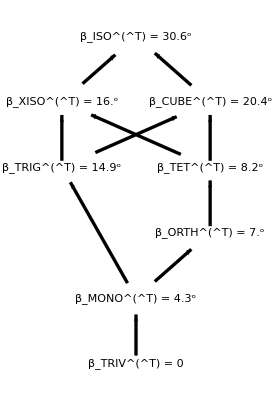

[T] = 1(10. | 0.7 | 1.05 | 5.2 | -3.92598 | -3.10269
0.7 | 8. | -2. | -0.2 | -0.46188 | 0.326599
1.05 | -2. | 6. | -0.45 | -0.190526 | 0.318434
5.2 | -0.2 | -0.45 | 5.5 | 0. | -1.22474
-3.92598 | -0.46188 | -0.190526 | 0. | 5.5 | 2.12132
-3.10269 | 0.326599 | 0.318434 | -1.22474 | 2.12132 | 13.)

#### TmatMar17

```mathematica
TmatPert=({{474, 22, 22, 18, 4, 10}, {22, 374, -22, 28, -16, -34}, {22, -22, 318, 6, -26, 6}, {18, 28, 6, 262, 8, 14}, {4, -16, -26, 8, 32, 42}, {10, -34, 6, 14, 42, 74}});
```

```mathematica
Urot=ZRot[-20.Degree].XRot[-30Degree];
TmatMar17=MatrixUbar[Urot].TmatPert.Transpose[MatrixUbar[Urot]];
MatrixLab[TmatMar17]="TmatMar17";
MatrixNote[TmatMar17]=fMatrixNote[MatrixLab[TmatMar17]];
PrintVoigt[TmatMar17];
```

The [T]_𝔹𝔹 matrix is (206.222 | -67.4376 | 17.062 | -15.8915 | 166.629 | -19.5016
-67.4376 | 352.858 | 32.2406 | 3.30383 | 61.6098 | -41.6251
17.062 | 32.2406 | 343.803 | 0.355839 | 73.5722 | -4.22981
-15.8915 | 3.30383 | 0.355839 | 269.972 | 88.7527 | 13.3226
166.629 | 61.6098 | 73.5722 | 88.7527 | 287.146 | 30.7189
-19.5016 | -41.6251 | -4.22981 | 13.3226 | 30.7189 | 74.)

The eigenvalues are: {483.05,387.082,311.329,256.996,91.5538,3.98966}

The Voigt matrix is (159.872 | -47.9805 | -32.4866 | 48.086 | -0.86007 | 19.3337
-47.9805 | 284.11 | -124.091 | 32.1945 | 2.44376 | 19.6896
-32.4866 | -124.091 | 187.135 | -104.165 | -52.5638 | -44.2037
48.086 | 32.1945 | -104.165 | 103.111 | -33.7188 | 8.53098
-0.86007 | 2.44376 | -52.5638 | -33.7188 | 176.429 | 16.1203
19.3337 | 19.6896 | -44.2037 | 8.53098 | 16.1203 | 171.902)

11-20-2023 15:51

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 350.348   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.49 = 28.06^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (292. | 0. | 0. | 0. | 0. | 0.
0. | 292. | 0. | 0. | 0. | 0.
0. | 0. | 292. | 0. | 0. | 0.
0. | 0. | 0. | 292. | 0. | 0.
0. | 0. | 0. | 0. | 292. | 0.
0. | 0. | 0. | 0. | 0. | 74.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = -72.6667 and μ = 146., Poisson is -0.495455

```mathematica
cmin=0;cmax=27; dc=3;
contours[TmatMar17]=Range[cmin,cmax,dc];
MaxForScaling[TmatMar17]=cmax-dc;
```

```mathematica
tpert[TmatMar17]=0.01;
```

#### lattice for TmatMar17:

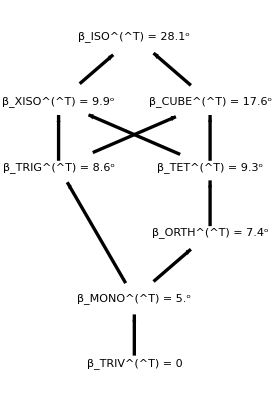

[T] = 1(206.222 | -67.4376 | 17.062 | -15.8915 | 166.629 | -19.5016
-67.4376 | 352.858 | 32.2406 | 3.30383 | 61.6098 | -41.6251
17.062 | 32.2406 | 343.803 | 0.355839 | 73.5722 | -4.22981
-15.8915 | 3.30383 | 0.355839 | 269.972 | 88.7527 | 13.3226
166.629 | 61.6098 | 73.5722 | 88.7527 | 287.146 | 30.7189
-19.5016 | -41.6251 | -4.22981 | 13.3226 | 30.7189 | 74.)

#### Brown, Angel, Ross (2016), Table 2, column 1 (pure albite) [units of GPa = 10^9 Pa = 10^9 N/m2] density is 2.623 g/cm^3 = 2623 kg/m^3

```mathematica
CmatBrown=({{68.3, 32.2, 30.4, 4.9, -2.3, -0.9}, {32.2, 184.3, 5., -4.4, -7.8, -6.4}, {30.4, 5., 180., -9.2, 7.5, -9.4}, {4.9, -4.4, -9.2, 25., -2.4, -7.2}, {-2.3, -7.8, 7.5, -2.4, 26.9, 0.6}, {-0.9, -6.4, -9.4, -7.2, 0.6, 33.6}});
TmatBrown = TmatOfCmat[CmatBrown];
MatrixLab[TmatBrown]="TmatBrown";
MatrixNote[TmatBrown]=fMatrixNote[MatrixLab[TmatBrown]];
PrintVoigt[TmatBrown];
```

The [T]_𝔹𝔹 matrix is (50. | -4.8 | -14.4 | -9.3 | 10.9119 | -7.10352
-4.8 | 53.8 | 1.2 | -5.5 | -14.4915 | -2.12289
-14.4 | 1.2 | 67.2 | -5.5 | 6.63953 | -13.6355
-9.3 | -5.5 | -5.5 | 94.1 | 48.151 | 36.9873
10.9119 | -14.4915 | 6.63953 | 48.151 | 149.233 | -18.4791
-7.10352 | -2.12289 | -13.6355 | 36.9873 | -18.4791 | 189.267)

The eigenvalues are: {204.263,179.169,75.8705,60.7101,50.1339,33.4538}

The Voigt matrix is (68.3 | 32.2 | 30.4 | 4.9 | -2.3 | -0.9
32.2 | 184.3 | 5. | -4.4 | -7.8 | -6.4
30.4 | 5. | 180. | -9.2 | 7.5 | -9.4
4.9 | -4.4 | -9.2 | 25. | -2.4 | -7.2
-2.3 | -7.8 | 7.5 | -2.4 | 26.9 | 0.6
-0.9 | -6.4 | -9.4 | -7.2 | 0.6 | 33.6)

11-20-2023 15:51

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 129.395   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.454 = 26.037^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

```mathematica
cmin=0;cmax=24; dc=3;
contours[TmatBrown]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrown]=cmax-dc;
```

```mathematica
tpert[TmatBrown]=0.66;
```

#### lattice for TmatBrown:

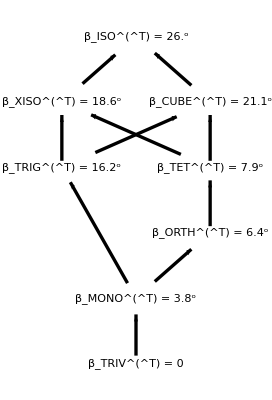

[T] = 1(50. | -4.8 | -14.4 | -9.3 | 10.9119 | -7.10352
-4.8 | 53.8 | 1.2 | -5.5 | -14.4915 | -2.12289
-14.4 | 1.2 | 67.2 | -5.5 | 6.63953 | -13.6355
-9.3 | -5.5 | -5.5 | 94.1 | 48.151 | 36.9873
10.9119 | -14.4915 | 6.63953 | 48.151 | 149.233 | -18.4791
-7.10352 | -2.12289 | -13.6355 | 36.9873 | -18.4791 | 189.267)

#### Original Brown matrix that we used (we had a typo in C34 as -39.2)

```mathematica
CmatBrownTypo=({{68.3, 32.2, 30.4, 4.9, -2.3, -0.9}, {32.2, 184.3, 5., -4.4, -7.8, -6.4}, {30.4, 5., 180., -39.2, 7.5, -9.4}, {4.9, -4.4, -39.2, 25., -2.4, -7.2}, {-2.3, -7.8, 7.5, -2.4, 26.9, 0.6}, {-0.9, -6.4, -9.4, -7.2, 0.6, 33.6}});
TmatBrownTypo = TmatOfCmat[CmatBrownTypo];
MatrixLab[TmatBrownTypo]="TmatBrownTypo";
MatrixNote[TmatBrownTypo]=fMatrixNote[MatrixLab[TmatBrownTypo]];
PrintVoigt[TmatBrownTypo];
```

The [T]_𝔹𝔹 matrix is (50. | -4.8 | -14.4 | -9.3 | 45.5529 | -31.5984
-4.8 | 53.8 | 1.2 | -5.5 | -14.4915 | -2.12289
-14.4 | 1.2 | 67.2 | -5.5 | 6.63953 | -13.6355
-9.3 | -5.5 | -5.5 | 94.1 | 48.151 | 36.9873
45.5529 | -14.4915 | 6.63953 | 48.151 | 149.233 | -18.4791
-31.5984 | -2.12289 | -13.6355 | 36.9873 | -18.4791 | 189.267)

The eigenvalues are: {213.687,186.256,75.2415,61.8659,51.3108,15.238}

The Voigt matrix is (68.3 | 32.2 | 30.4 | 4.9 | -2.3 | -0.9
32.2 | 184.3 | 5. | -4.4 | -7.8 | -6.4
30.4 | 5. | 180. | -39.2 | 7.5 | -9.4
4.9 | -4.4 | -39.2 | 25. | -2.4 | -7.2
-2.3 | -7.8 | 7.5 | -2.4 | 26.9 | 0.6
-0.9 | -6.4 | -9.4 | -7.2 | 0.6 | 33.6)

11-20-2023 15:51

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 150.17   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.516 = 29.55^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (82.8667 | 0. | 0. | 0. | 0. | 0.
0. | 82.8667 | 0. | 0. | 0. | 0.
0. | 0. | 82.8667 | 0. | 0. | 0.
0. | 0. | 0. | 82.8667 | 0. | 0.
0. | 0. | 0. | 0. | 82.8667 | 0.
0. | 0. | 0. | 0. | 0. | 189.267)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 35.4667 and μ = 41.4333, Poisson is 0.230603

```mathematica
cmin=0;cmax=27; dc=3;
contours[TmatBrownTypo]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownTypo]=cmax-dc;
```

```mathematica
tpert[TmatBrownTypo]=0.22;
```

#### Map used in SSA2023 by Aakash Gupta, generated from ES_FarFromMono.nb

```mathematica
TmatSSA2023=({{0.317082, -0.00658517, 0.227862, 0.219176, 0.114762, -0.244823}, {-0.00658517, 0.07346, -0.114858, -0.0207015, 0.0275774, -0.142342}, {0.227862, -0.114858, 0.420424, 0.212793, 0.0528639, 0.120438}, {0.219176, -0.0207015, 0.212793, 0.241031, 0.102265, -0.162818}, {0.114762, 0.0275774, 0.0528639, 0.102265, 0.0962717, -0.147361}, {-0.244823, -0.142342, 0.120438, -0.162818, -0.147361, 0.64901}});
```

```mathematica
MatrixLab[TmatSSA2023]="TmatSSA2023";
MatrixNote[TmatSSA2023]=fMatrixNote[MatrixLab[TmatSSA2023]];
PrintVoigt[TmatSSA2023];
```

The [T]_𝔹𝔹 matrix is (0.317082 | -0.00658517 | 0.227862 | 0.219176 | 0.114762 | -0.244823
-0.00658517 | 0.07346 | -0.114858 | -0.0207015 | 0.0275774 | -0.142342
0.227862 | -0.114858 | 0.420424 | 0.212793 | 0.0528639 | 0.120438
0.219176 | -0.0207015 | 0.212793 | 0.241031 | 0.102265 | -0.162818
0.114762 | 0.0275774 | 0.0528639 | 0.102265 | 0.0962717 | -0.147361
-0.244823 | -0.142342 | 0.120438 | -0.162818 | -0.147361 | 0.64901)

The eigenvalues are: {0.965054,0.701544,0.060227,0.0422136,0.0158499,0.0123903}

The Voigt matrix is (0.357328 | 0.0423998 | 0.344492 | -0.176408 | -0.0397992 | -0.0419674
0.0423998 | 0.209533 | 0.0934665 | 0.0427684 | -0.0605007 | 0.170826
0.344492 | 0.0934665 | 0.419451 | -0.166206 | -0.0740327 | 0.0186476
-0.176408 | 0.0427684 | -0.166206 | 0.158541 | -0.00329258 | 0.113931
-0.0397992 | -0.0605007 | -0.0740327 | -0.00329258 | 0.03673 | -0.057429
-0.0419674 | 0.170826 | 0.0186476 | 0.113931 | -0.057429 | 0.210212)

11-20-2023 15:51

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 0.86278   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.806 = 46.19^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (0.229654 | 0. | 0. | 0. | 0. | 0.
0. | 0.229654 | 0. | 0. | 0. | 0.
0. | 0. | 0.229654 | 0. | 0. | 0.
0. | 0. | 0. | 0.229654 | 0. | 0.
0. | 0. | 0. | 0. | 0.229654 | 0.
0. | 0. | 0. | 0. | 0. | 0.64901)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 0.139785 and μ = 0.114827, Poisson is 0.274506

```mathematica
cmin=0;cmax=40; dc=4;
contours[TmatSSA2023]=Range[cmin,cmax,dc];
MaxForScaling[TmatSSA2023]=cmax-dc;
```

```mathematica
tpert[TmatSSA2023]=0.04;
```

#### lattice for TmatSSA2023:

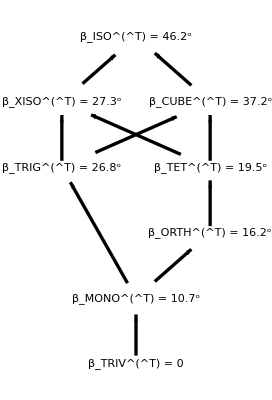

[T] = 1(0.317082 | -0.00658517 | 0.227862 | 0.219176 | 0.114762 | -0.244823
-0.00658517 | 0.07346 | -0.114858 | -0.0207015 | 0.0275774 | -0.142342
0.227862 | -0.114858 | 0.420424 | 0.212793 | 0.0528639 | 0.120438
0.219176 | -0.0207015 | 0.212793 | 0.241031 | 0.102265 | -0.162818
0.114762 | 0.0275774 | 0.0528639 | 0.102265 | 0.0962717 | -0.147361
-0.244823 | -0.142342 | 0.120438 | -0.162818 | -0.147361 | 0.64901)

#### Russell, Gaherty, et al. (2019 JGR), Table 1 [units of GPa = 10^9 Pa = 10^9 N/m2]

```mathematica
CmatRussell=({{271.6149, 101.6837, 101.2700, 0, 0, −0.1902}, {101.6837, 233.9946, 99.9429, 0, 0, 0.3918}, {101.2700, 99.9429, 239.5542, 0, 0, 0.0071}, {0, 0, 0, 66.1769, 0.0452, 0}, {0, 0, 0, 0.0452, 74.6177, 0}, {−0.1902, 0.3918, 0.0071, 0, 0, 71.9655}});
TmatRussell = TmatOfCmat[CmatRussell];
MatrixLab[TmatRussell]="TmatRussell";
MatrixNote[TmatRussell]=fMatrixNote[MatrixLab[TmatRussell]];
PrintVoigt[TmatRussell];
```

The [T]_𝔹𝔹 matrix is (132.354 | 0.0904 | 0 | 0 | 0 | 0
0.0904 | 149.235 | 0 | 0 | 0 | 0
0 | 0 | 143.931 | 0.582 | 0.108195 | 0.170403
0 | 0 | 0.582 | 151.121 | -10.0938 | -15.9002
0 | 0 | 0.108195 | -10.0938 | 143.724 | 6.75419
0 | 0 | 0.170403 | -15.9002 | 6.75419 | 450.319)

The eigenvalues are: {451.334,157.213,149.236,143.943,136.605,132.353}

The Voigt matrix is (271.615 | 101.684 | 101.27 | 0 | 0 | -0.1902
101.684 | 233.995 | 99.9429 | 0 | 0 | 0.3918
101.27 | 99.9429 | 239.554 | 0 | 0 | 0.0071
0 | 0 | 0 | 66.1769 | 0.0452 | 0
0 | 0 | 0 | 0.0452 | 74.6177 | 0
-0.1902 | 0.3918 | 0.0071 | 0 | 0 | 71.9655)

11-20-2023 15:51

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 31.8626   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.057 = 3.29^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (144.073 | 0. | 0. | 0. | 0. | 0.
0. | 144.073 | 0. | 0. | 0. | 0.
0. | 0. | 144.073 | 0. | 0. | 0.
0. | 0. | 0. | 144.073 | 0. | 0.
0. | 0. | 0. | 0. | 144.073 | 0.
0. | 0. | 0. | 0. | 0. | 450.319)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 102.082 and μ = 72.0365, Poisson is 0.293139

```mathematica
cmin=0;cmax=3.25; dc=0.25;
contours[TmatRussell]=Range[cmin,cmax,dc];
MaxForScaling[TmatRussell]=cmax-dc;
```

```mathematica
tpert[TmatRussell]=11.29;
```

#### lattice for TmatRussell:

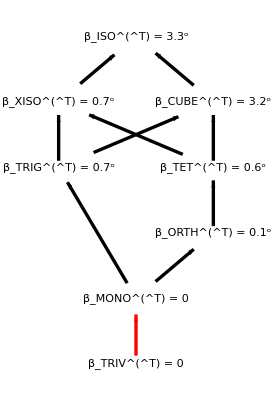

[T] = 1(132.354 | 0.0904 | 0. | 0. | 0. | 0.
0.0904 | 149.235 | 0. | 0. | 0. | 0.
0. | 0. | 143.931 | 0.582 | 0.108195 | 0.170403
0. | 0. | 0.582 | 151.121 | -10.0938 | -15.9002
0. | 0. | 0.108195 | -10.0938 | 143.724 | 6.75419
0. | 0. | 0.170403 | -15.9002 | 6.75419 | 450.319)

## Maps from Tape and Tape (2021)

#### TRIV (Eq. 23)

```mathematica
denominator=5;
TT21TRIV=1/denominator({{5, 0, 0, -2, 0, 0}, {0, 6, 0, 0, -2, 0}, {0, 0, 5, 0, 0, 0}, {-2, 0, 0, 5, 0, 0}, {0, -2, 0, 0, 6, 0}, {0, 0, 0, 0, 0, 6}});
```

```mathematica
MatrixNote[TT21TRIV]="Tmat is TT21TRIV";
PrintVoigt[TT21TRIV];
```

The [T]_𝔹𝔹 matrix is (1 | 0 | 0 | -2/5 | 0 | 0
0 | 6/5 | 0 | 0 | -2/5 | 0
0 | 0 | 1 | 0 | 0 | 0
-2/5 | 0 | 0 | 1 | 0 | 0
0 | -2/5 | 0 | 0 | 6/5 | 0
0 | 0 | 0 | 0 | 0 | 6/5)

The eigenvalues are: {8/5,7/5,6/5,1,4/5,3/5}

The Voigt matrix is (11/10 | 1/10 | 0 | 1/5 | -1/(5 √3) | 0
1/10 | 11/10 | 0 | -1/5 | -1/(5 √3) | 0
0 | 0 | 6/5 | 0 | 2/(5 √3) | 0
1/5 | -1/5 | 0 | 1/2 | 0 | 0
-1/(5 √3) | -1/(5 √3) | 2/(5 √3) | 0 | 3/5 | 0
0 | 0 | 0 | 0 | 0 | 1/2)

11-20-2023 15:51

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = (√(86/5))/5   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.298 = 17.1^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (1.08 | 0. | 0. | 0. | 0. | 0.
0. | 1.08 | 0. | 0. | 0. | 0.
0. | 0. | 1.08 | 0. | 0. | 0.
0. | 0. | 0. | 1.08 | 0. | 0.
0. | 0. | 0. | 0. | 1.08 | 0.
0. | 0. | 0. | 0. | 0. | 1.2)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 1/25 and μ = 27/50, Poisson is 1/29

#### lattice for TT21TRIV:

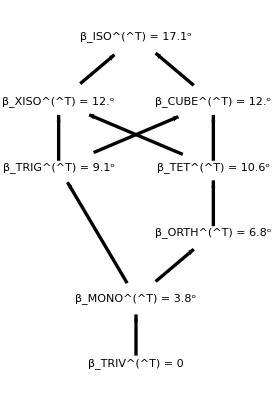

[T] = 1/5(5 | 0 | 0 | -2 | 0 | 0
0 | 6 | 0 | 0 | -2 | 0
0 | 0 | 5 | 0 | 0 | 0
-2 | 0 | 0 | 5 | 0 | 0
0 | -2 | 0 | 0 | 6 | 0
0 | 0 | 0 | 0 | 0 | 6)

#### MONO (Section 15.1)

```mathematica
denominator=80;
TT21MONO=1/denominator({{222, -12 √6, -82, 21 √6, -39 √2, 0}, {-12 √6, 196, 12 √6, 30, 10 √3, -16}, {-82, 12 √6, 222, 9 √6, -51 √2, 0}, {21 √6, 30, 9 √6, 242, -6 √3, -24}, {-39 √2, 10 √3, -51 √2, -6 √3, 254, -8 √3}, {0, -16, 0, -24, -8 √3, 304}});
```

```mathematica
MatrixNote[TT21MONO]="Tmat is TT21MONO";
PrintVoigt[TT21MONO];
MatrixForm[N[TT21MONO]]
```

The [T]_𝔹𝔹 matrix is (111/40 | -(3 √(3/2))/10 | -41/40 | (21 √(3/2))/40 | -39/(40 √2) | 0
-(3 √(3/2))/10 | 49/20 | (3 √(3/2))/10 | 3/8 | (√3)/8 | -1/5
-41/40 | (3 √(3/2))/10 | 111/40 | (9 √(3/2))/40 | -51/(40 √2) | 0
(21 √(3/2))/40 | 3/8 | (9 √(3/2))/40 | 121/40 | -(3 √3)/40 | -3/10
-39/(40 √2) | (√3)/8 | -51/(40 √2) | -(3 √3)/40 | 127/40 | -(√3)/10
0 | -1/5 | 0 | -3/10 | -(√3)/10 | 19/5)

The eigenvalues are: {4,4,4,3,2,1}

The Voigt matrix is (1/60 (203+4 √6) | 1/60 (17-2 √6) | 1/15 (2+√6) | -(17 √(3/2))/40 | -1/8-1/(5 √6) | -(13 √(3/2))/40
1/60 (17-2 √6) | 1/30 (97-4 √6) | 1/60 (17-2 √6) | (√(3/2))/10 | 1/4-1/(5 √6) | -(√(3/2))/10
1/15 (2+√6) | 1/60 (17-2 √6) | 1/60 (203+4 √6) | (13 √(3/2))/40 | -1/8-1/(5 √6) | (17 √(3/2))/40
-(17 √(3/2))/40 | (√(3/2))/10 | (13 √(3/2))/40 | 111/80 | -(3 √(3/2))/20 | -41/80
-1/8-1/(5 √6) | 1/4-1/(5 √6) | -1/8-1/(5 √6) | -(3 √(3/2))/20 | 49/40 | (3 √(3/2))/20
-(13 √(3/2))/40 | -(√(3/2))/10 | (17 √(3/2))/40 | -41/80 | (3 √(3/2))/20 | 111/80)

11-20-2023 15:51

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = (2 √(226/5))/5   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.349 = 19.97^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (2.84 | 0. | 0. | 0. | 0. | 0.
0. | 2.84 | 0. | 0. | 0. | 0.
0. | 0. | 2.84 | 0. | 0. | 0.
0. | 0. | 0. | 2.84 | 0. | 0.
0. | 0. | 0. | 0. | 2.84 | 0.
0. | 0. | 0. | 0. | 0. | 3.8)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 8/25 and μ = 71/50, Poisson is 8/87

(2.775 | -0.367423 | -1.025 | 0.642991 | -0.689429 | 0.
-0.367423 | 2.45 | 0.367423 | 0.375 | 0.216506 | -0.2
-1.025 | 0.367423 | 2.775 | 0.275568 | -0.901561 | 0.
0.642991 | 0.375 | 0.275568 | 3.025 | -0.129904 | -0.3
-0.689429 | 0.216506 | -0.901561 | -0.129904 | 3.175 | -0.173205
0. | -0.2 | 0. | -0.3 | -0.173205 | 3.8)

#### lattice for TT21MONO:

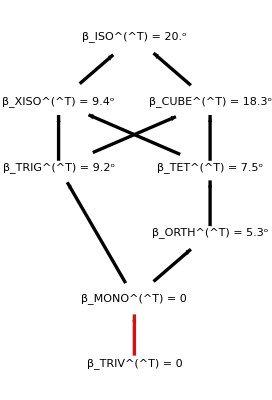

[T] = 1/80(222 | -12 √6 | -82 | 21 √6 | -39 √2 | 0
-12 √6 | 196 | 12 √6 | 30 | 10 √3 | -16
-82 | 12 √6 | 222 | 9 √6 | -51 √2 | 0
21 √6 | 30 | 9 √6 | 242 | -6 √3 | -24
-39 √2 | 10 √3 | -51 √2 | -6 √3 | 254 | -8 √3
0 | -16 | 0 | -24 | -8 √3 | 304)

#### ORTH (Section 15.2)

```mathematica
denominator=10;
TT21ORTH=1/denominator({{38, 18, 3 √2, -5 √2, -√6, -√8}, {18, 38, 3 √2, 5 √2, -√6, -√8}, {3 √2, 3 √2, 41, 0, -7 √3, 6}, {-5 √2, 5 √2, 0, 20, 0, 0}, {-√6, -√6, -7 √3, 0, 27, -2 √3}, {-√8, -√8, 6, 0, -2 √3, 56}});
```

```mathematica
MatrixNote[TT21ORTH]="Tmat is TT21ORTH";
PrintVoigt[TT21ORTH];
MatrixForm[N[TT21ORTH]]
```

The [T]_𝔹𝔹 matrix is (19/5 | 9/5 | 3/(5 √2) | -1/(√2) | -(√(3/2))/5 | -(√2)/5
9/5 | 19/5 | 3/(5 √2) | 1/(√2) | -(√(3/2))/5 | -(√2)/5
3/(5 √2) | 3/(5 √2) | 41/10 | 0 | -(7 √3)/10 | 3/5
-1/(√2) | 1/(√2) | 0 | 2 | 0 | 0
-(√(3/2))/5 | -(√(3/2))/5 | -(7 √3)/10 | 0 | 27/10 | -(√3)/5
-(√2)/5 | -(√2)/5 | 3/5 | 0 | -(√3)/5 | 28/5)

The eigenvalues are: {6,6,4,3,2,1}

The Voigt matrix is (1/60 (199-4 √6) | 1/60 (79-4 √6) | 1/30 (29+√6) | -(-6+√6)/(15 √2) | -(9+√6)/(15 √2) | 1/20 (-7+2 √6)
1/60 (79-4 √6) | 1/60 (199-4 √6) | 1/30 (29+√6) | -(9+√6)/(15 √2) | -(-6+√6)/(15 √2) | 1/20 (-7+2 √6)
1/30 (29+√6) | 1/30 (29+√6) | 1/15 (55+2 √6) | -(-3+√6)/(15 √2) | -(-3+√6)/(15 √2) | 1/10 (7+√6)
-(-6+√6)/(15 √2) | -(9+√6)/(15 √2) | -(-3+√6)/(15 √2) | 19/10 | 9/10 | 3/(10 √2)
-(9+√6)/(15 √2) | -(-6+√6)/(15 √2) | -(-3+√6)/(15 √2) | 9/10 | 19/10 | 3/(10 √2)
1/20 (-7+2 √6) | 1/20 (-7+2 √6) | 1/10 (7+√6) | 3/(10 √2) | 3/(10 √2) | 41/20)

11-20-2023 15:51

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = (9 √(26/5))/5   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.419 = 23.98^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (3.28 | 0. | 0. | 0. | 0. | 0.
0. | 3.28 | 0. | 0. | 0. | 0.
0. | 0. | 3.28 | 0. | 0. | 0.
0. | 0. | 0. | 3.28 | 0. | 0.
0. | 0. | 0. | 0. | 3.28 | 0.
0. | 0. | 0. | 0. | 0. | 5.6)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 58/75 and μ = 41/25, Poisson is 29/181

(3.8 | 1.8 | 0.424264 | -0.707107 | -0.244949 | -0.282843
1.8 | 3.8 | 0.424264 | 0.707107 | -0.244949 | -0.282843
0.424264 | 0.424264 | 4.1 | 0. | -1.21244 | 0.6
-0.707107 | 0.707107 | 0. | 2. | 0. | 0.
-0.244949 | -0.244949 | -1.21244 | 0. | 2.7 | -0.34641
-0.282843 | -0.282843 | 0.6 | 0. | -0.34641 | 5.6)

#### lattice for TT21ORTH:

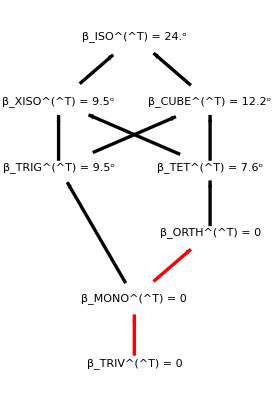

[T] = 1/10(38 | 18 | 3 √2 | -5 √2 | -√6 | -2 √2
18 | 38 | 3 √2 | 5 √2 | -√6 | -2 √2
3 √2 | 3 √2 | 41 | 0 | -7 √3 | 6
-5 √2 | 5 √2 | 0 | 20 | 0 | 0
-√6 | -√6 | -7 √3 | 0 | 27 | -2 √3
-2 √2 | -2 √2 | 6 | 0 | -2 √3 | 56)

#### TET (Section 15.3)

```mathematica
denominator=64;
TT21TET=1/denominator({{168, 4 √6, -40, 6 √6, 6 √2, 0}, {4 √6, 324, -4 √6, -42, -14 √3, 16 √3}, {-40, -4 √6, 168, -6 √6, -6 √2, 0}, {6 √6, -42, -6 √6, 233, 35 √3, -8 √3}, {6 √2, -14 √3, -6 √2, 35 √3, 163, -8}, {0, 16 √3, 0, -8 √3, -8, 352}});
```

```mathematica
MatrixNote[TT21TET]="Tmat is TT21TET";
PrintVoigt[TT21TET];
MatrixForm[N[TT21TET]]
```

The [T]_𝔹𝔹 matrix is (21/8 | (√(3/2))/8 | -5/8 | (3 √(3/2))/16 | 3/(16 √2) | 0
(√(3/2))/8 | 81/16 | -(√(3/2))/8 | -21/32 | -(7 √3)/32 | (√3)/4
-5/8 | -(√(3/2))/8 | 21/8 | -(3 √(3/2))/16 | -3/(16 √2) | 0
(3 √(3/2))/16 | -21/32 | -(3 √(3/2))/16 | 233/64 | (35 √3)/64 | -(√3)/8
3/(16 √2) | -(7 √3)/32 | -3/(16 √2) | (35 √3)/64 | 163/64 | -1/8
0 | (√3)/4 | 0 | -(√3)/8 | -1/8 | 11/2)

The eigenvalues are: {6,5,4,3,2,2}

The Voigt matrix is (1/96 (339+8 √2) | 1/48 (21-2 √2) | 1/96 (147+8 √2) | -(√(3/2))/16 | 1/32 (7+4 √2) | (√(3/2))/16
1/48 (21-2 √2) | 37/8-1/(3 √2) | 1/48 (21-2 √2) | (√(3/2))/8 | 1/16 (-7+2 √2) | -(√(3/2))/8
1/96 (147+8 √2) | 1/48 (21-2 √2) | 1/96 (339+8 √2) | -(√(3/2))/16 | 1/32 (7+4 √2) | (√(3/2))/16
-(√(3/2))/16 | (√(3/2))/8 | -(√(3/2))/16 | 21/16 | (√(3/2))/16 | -5/16
1/32 (7+4 √2) | 1/16 (-7+2 √2) | 1/32 (7+4 √2) | (√(3/2))/16 | 81/32 | -(√(3/2))/16
(√(3/2))/16 | -(√(3/2))/8 | (√(3/2))/16 | -5/16 | -(√(3/2))/16 | 21/16)

11-20-2023 15:51

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = √(93/10)   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.32 = 18.33^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (3.3 | 0. | 0. | 0. | 0. | 0.
0. | 3.3 | 0. | 0. | 0. | 0.
0. | 0. | 3.3 | 0. | 0. | 0.
0. | 0. | 0. | 3.3 | 0. | 0.
0. | 0. | 0. | 0. | 3.3 | 0.
0. | 0. | 0. | 0. | 0. | 5.5)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 11/15 and μ = 33/20, Poisson is 2/13

(2.625 | 0.153093 | -0.625 | 0.22964 | 0.132583 | 0.
0.153093 | 5.0625 | -0.153093 | -0.65625 | -0.378886 | 0.433013
-0.625 | -0.153093 | 2.625 | -0.22964 | -0.132583 | 0.
0.22964 | -0.65625 | -0.22964 | 3.64063 | 0.947215 | -0.216506
0.132583 | -0.378886 | -0.132583 | 0.947215 | 2.54688 | -0.125
0. | 0.433013 | 0. | -0.216506 | -0.125 | 5.5)

#### lattice for TT21TET:

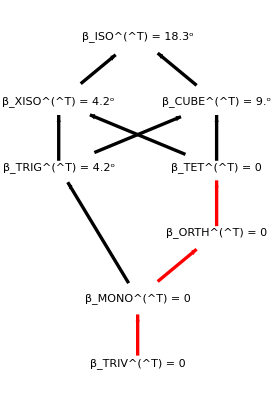

[T] = 1/64(168 | 4 √6 | -40 | 6 √6 | 6 √2 | 0
4 √6 | 324 | -4 √6 | -42 | -14 √3 | 16 √3
-40 | -4 √6 | 168 | -6 √6 | -6 √2 | 0
6 √6 | -42 | -6 √6 | 233 | 35 √3 | -8 √3
6 √2 | -14 √3 | -6 √2 | 35 √3 | 163 | -8
0 | 16 √3 | 0 | -8 √3 | -8 | 352)

#### XISO (Section 15.4)

```mathematica
denominator=128;
TT21XISO=1/denominator({{532, 92 √3, 122, -2 √3, -60, 48}, {92 √3, 348, -2 √3, 126, -20 √3, 16 √3}, {122, -2 √3, 349, 31 √3, -126, 24}, {-2 √3, 126, 31 √3, 287, -42 √3, 8 √3}, {-60, -20 √3, -126, -42 √3, 212, -16}, {48, 16 √3, 24, 8 √3, -16, 704}});
```

```mathematica
MatrixNote[TT21XISO]="Tmat is TT21XISO";
PrintVoigt[TT21XISO];
MatrixForm[N[TT21XISO]]
```

The [T]_𝔹𝔹 matrix is (133/32 | (23 √3)/32 | 61/64 | -(√3)/64 | -15/32 | 3/8
(23 √3)/32 | 87/32 | -(√3)/64 | 63/64 | -(5 √3)/32 | (√3)/8
61/64 | -(√3)/64 | 349/128 | (31 √3)/128 | -63/64 | 3/16
-(√3)/64 | 63/64 | (31 √3)/128 | 287/128 | -(21 √3)/64 | (√3)/16
-15/32 | -(5 √3)/32 | -63/64 | -(21 √3)/64 | 53/32 | -1/8
3/8 | (√3)/8 | 3/16 | (√3)/16 | -1/8 | 11/2)

The eigenvalues are: {6,5,3,3,1,1}

The Voigt matrix is (1/768 (2733-80 √2) | 1/768 (759-32 √2) | 1/192 (183-2 √2) | 1/128 √3 (-9+8 √2) | 1/128 (-73+8 √2) | 1/256 √3 (-73+8 √2)
1/768 (759-32 √2) | 1/768 (2229+16 √2) | 1/192 (309+10 √2) | 1/128 √3 (-11+8 √2) | 1/128 (53+8 √2) | 1/256 √3 (-11+8 √2)
1/192 (183-2 √2) | 1/192 (309+10 √2) | 1/48 (141+4 √2) | 1/32 √(3/2) (4+5 √2) | 1/32 (5+2 √2) | 1/64 √(3/2) (4+21 √2)
1/128 √3 (-9+8 √2) | 1/128 √3 (-11+8 √2) | 1/32 √(3/2) (4+5 √2) | 133/64 | (23 √3)/64 | 61/128
1/128 (-73+8 √2) | 1/128 (53+8 √2) | 1/32 (5+2 √2) | (23 √3)/64 | 87/64 | -(√3)/128
1/256 √3 (-73+8 √2) | 1/256 √3 (-11+8 √2) | 1/64 √(3/2) (4+21 √2) | 61/128 | -(√3)/128 | 349/256)

11-20-2023 15:51

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = √(143/10)   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.434 = 24.85^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (2.7 | 0. | 0. | 0. | 0. | 0.
0. | 2.7 | 0. | 0. | 0. | 0.
0. | 0. | 2.7 | 0. | 0. | 0.
0. | 0. | 0. | 2.7 | 0. | 0.
0. | 0. | 0. | 0. | 2.7 | 0.
0. | 0. | 0. | 0. | 0. | 5.5)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 14/15 and μ = 27/20, Poisson is 28/137

(4.15625 | 1.24491 | 0.953125 | -0.0270633 | -0.46875 | 0.375
1.24491 | 2.71875 | -0.0270633 | 0.984375 | -0.270633 | 0.216506
0.953125 | -0.0270633 | 2.72656 | 0.419481 | -0.984375 | 0.1875
-0.0270633 | 0.984375 | 0.419481 | 2.24219 | -0.568329 | 0.108253
-0.46875 | -0.270633 | -0.984375 | -0.568329 | 1.65625 | -0.125
0.375 | 0.216506 | 0.1875 | 0.108253 | -0.125 | 5.5)

#### lattice for TT21XISO:

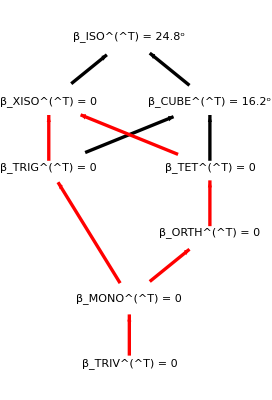

[T] = 1/128(532 | 92 √3 | 122 | -2 √3 | -60 | 48
92 √3 | 348 | -2 √3 | 126 | -20 √3 | 16 √3
122 | -2 √3 | 349 | 31 √3 | -126 | 24
-2 √3 | 126 | 31 √3 | 287 | -42 √3 | 8 √3
-60 | -20 √3 | -126 | -42 √3 | 212 | -16
48 | 16 √3 | 24 | 8 √3 | -16 | 704)

#### CUBE (Section 15.5)

```mathematica
denominator=36;
TT21CUBE=1/denominator({{52, 4, 16, -6, -2 √3, 0}, {4, 64, 4, 12, 4 √3, 0}, {16, 4, 52, -6, -2 √3, 0}, {-6, 12, -6, 45, 3 √3, 0}, {-2 √3, 4 √3, -2 √3, 3 √3, 39, 0}, {0, 0, 0, 0, 0, 108}});
```

```mathematica
MatrixNote[TT21CUBE]="Tmat is TT21CUBE";
PrintVoigt[TT21CUBE];
MatrixForm[N[TT21CUBE]]
```

The [T]_𝔹𝔹 matrix is (13/9 | 1/9 | 4/9 | -1/6 | -1/(6 √3) | 0
1/9 | 16/9 | 1/9 | 1/3 | 1/(3 √3) | 0
4/9 | 1/9 | 13/9 | -1/6 | -1/(6 √3) | 0
-1/6 | 1/3 | -1/6 | 5/4 | 1/(4 √3) | 0
-1/(6 √3) | 1/(3 √3) | -1/(6 √3) | 1/(4 √3) | 13/12 | 0
0 | 0 | 0 | 0 | 0 | 3)

The eigenvalues are: {3,2,2,1,1,1}

The Voigt matrix is (31/18 | 5/9 | 13/18 | 1/18 | -1/9 | 1/18
5/9 | 17/9 | 5/9 | -1/9 | 2/9 | -1/9
13/18 | 5/9 | 31/18 | 1/18 | -1/9 | 1/18
1/18 | -1/9 | 1/18 | 13/18 | 1/18 | 2/9
-1/9 | 2/9 | -1/9 | 1/18 | 8/9 | 1/18
1/18 | -1/9 | 1/18 | 2/9 | 1/18 | 13/18)

11-20-2023 15:51

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = √(6/5)   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.247 = 14.18^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (1.4 | 0. | 0. | 0. | 0. | 0.
0. | 1.4 | 0. | 0. | 0. | 0.
0. | 0. | 1.4 | 0. | 0. | 0.
0. | 0. | 0. | 1.4 | 0. | 0.
0. | 0. | 0. | 0. | 1.4 | 0.
0. | 0. | 0. | 0. | 0. | 3.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 8/15 and μ = 7/10, Poisson is 8/37

(1.44444 | 0.111111 | 0.444444 | -0.166667 | -0.096225 | 0.
0.111111 | 1.77778 | 0.111111 | 0.333333 | 0.19245 | 0.
0.444444 | 0.111111 | 1.44444 | -0.166667 | -0.096225 | 0.
-0.166667 | 0.333333 | -0.166667 | 1.25 | 0.144338 | 0.
-0.096225 | 0.19245 | -0.096225 | 0.144338 | 1.08333 | 0.
0. | 0. | 0. | 0. | 0. | 3.)

#### lattice for TT21CUBE:

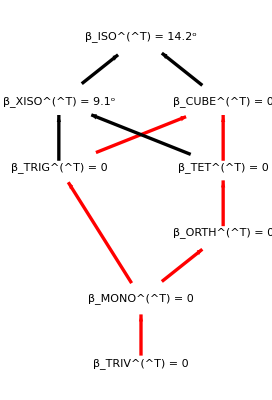

[T] = 1/36(52 | 4 | 16 | -6 | -2 √3 | 0
4 | 64 | 4 | 12 | 4 √3 | 0
16 | 4 | 52 | -6 | -2 √3 | 0
-6 | 12 | -6 | 45 | 3 √3 | 0
-2 √3 | 4 √3 | -2 √3 | 3 √3 | 39 | 0
0 | 0 | 0 | 0 | 0 | 108)

#### TRIG (Section 15.6)

```mathematica
denominator=16;
TT21TRIG=1/denominator({{4(8-√3), -8, 3 √2, -6 √2, -3 √6, 0}, {-8, 4(8+√3), 3 √2, 6 √2, -3 √6, 0}, {3 √2, 3 √2, 76, -2 √3, 12 √3, 4 √3}, {-6 √2, 6 √2, -2 √3, 24, 6, 0}, {-3 √6, -3 √6, 12 √3, 6, 52, 4}, {0, 0, 4 √3, 0, 4, 88}});
```

```mathematica
MatrixNote[TT21TRIG]="Tmat is TT21TRIG";
PrintVoigt[TT21TRIG];
MatrixForm[N[TT21TRIG]]
```

The [T]_𝔹𝔹 matrix is (1/4 (8-√3) | -1/2 | 3/(8 √2) | -3/(4 √2) | -(3 √(3/2))/8 | 0
-1/2 | 1/4 (8+√3) | 3/(8 √2) | 3/(4 √2) | -(3 √(3/2))/8 | 0
3/(8 √2) | 3/(8 √2) | 19/4 | -(√3)/8 | (3 √3)/4 | (√3)/4
-3/(4 √2) | 3/(4 √2) | -(√3)/8 | 3/2 | 3/8 | 0
-(3 √(3/2))/8 | -(3 √(3/2))/8 | (3 √3)/4 | 3/8 | 13/4 | 1/4
0 | 0 | (√3)/4 | 0 | 1/4 | 11/2)

The eigenvalues are: {6,5,3,3,1,1}

The Voigt matrix is (1/24 (75+2 √2-3 √3) | 1/24 (39+2 √2) | 1/24 (18-√2+3 √3) | 3/(16 √2) | -9/(16 √2) | 1/16 (6+2 √2+√3)
1/24 (39+2 √2) | 1/24 (75+2 √2+3 √3) | 1/24 (18-√2-3 √3) | -9/(16 √2) | 3/(16 √2) | 1/16 (6+2 √2-√3)
1/24 (18-√2+3 √3) | 1/24 (18-√2-3 √3) | 4-1/(3 √2) | 3/(8 √2) | 3/(8 √2) | 1/8 (-6+√2)
3/(16 √2) | -9/(16 √2) | 3/(8 √2) | 1-(√3)/8 | -1/4 | 3/(16 √2)
-9/(16 √2) | 3/(16 √2) | 3/(8 √2) | -1/4 | 1/8 (8+√3) | 3/(16 √2)
1/16 (6+2 √2+√3) | 1/16 (6+2 √2-√3) | 1/8 (-6+√2) | 3/(16 √2) | 3/(16 √2) | 19/8)

11-20-2023 15:51

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = √(143/10)   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.434 = 24.85^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (2.7 | 0. | 0. | 0. | 0. | 0.
0. | 2.7 | 0. | 0. | 0. | 0.
0. | 0. | 2.7 | 0. | 0. | 0.
0. | 0. | 0. | 2.7 | 0. | 0.
0. | 0. | 0. | 0. | 2.7 | 0.
0. | 0. | 0. | 0. | 0. | 5.5)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 14/15 and μ = 27/20, Poisson is 28/137

(1.56699 | -0.5 | 0.265165 | -0.53033 | -0.459279 | 0.
-0.5 | 2.43301 | 0.265165 | 0.53033 | -0.459279 | 0.
0.265165 | 0.265165 | 4.75 | -0.216506 | 1.29904 | 0.433013
-0.53033 | 0.53033 | -0.216506 | 1.5 | 0.375 | 0.
-0.459279 | -0.459279 | 1.29904 | 0.375 | 3.25 | 0.25
0. | 0. | 0.433013 | 0. | 0.25 | 5.5)

#### lattice for TT21TRIG:

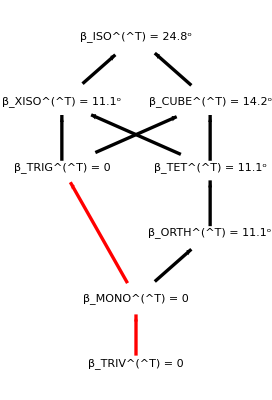

[T] = 1/16(4 (8-√3) | -8 | 3 √2 | -6 √2 | -3 √6 | 0
-8 | 4 (8+√3) | 3 √2 | 6 √2 | -3 √6 | 0
3 √2 | 3 √2 | 76 | -2 √3 | 12 √3 | 4 √3
-6 √2 | 6 √2 | -2 √3 | 24 | 6 | 0
-3 √6 | -3 √6 | 12 √3 | 6 | 52 | 4
0 | 0 | 4 √3 | 0 | 4 | 88)

#### ISO (there is no example in TT21; this is from elastic_mapping_iso.nb)

```mathematica
TT21ISO=({{3, 0, 0, 0, 0, 0}, {0, 3, 0, 0, 0, 0}, {0, 0, 3, 0, 0, 0}, {0, 0, 0, 3, 0, 0}, {0, 0, 0, 0, 3, 0}, {0, 0, 0, 0, 0, 1}});
```

```mathematica
MatrixNote[TT21ISO]="Tmat is TT21ISO";
PrintVoigt[TT21ISO];
MatrixForm[N[TT21ISO]]
```

The [T]_𝔹𝔹 matrix is (3 | 0 | 0 | 0 | 0 | 0
0 | 3 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0
0 | 0 | 0 | 0 | 0 | 1)

The eigenvalues are: {3,3,3,3,3,1}

The Voigt matrix is (7/3 | -2/3 | -2/3 | 0 | 0 | 0
-2/3 | 7/3 | -2/3 | 0 | 0 | 0
-2/3 | -2/3 | 7/3 | 0 | 0 | 0
0 | 0 | 0 | 3/2 | 0 | 0
0 | 0 | 0 | 0 | 3/2 | 0
0 | 0 | 0 | 0 | 0 | 3/2)

11-20-2023 15:51

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 0   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0, (Angle betweem T and 𝒯_ISO)

Since β_ISO^(□  T) = 0, then T is assigned symmetry ISO.

Lamé parameters for T are λ = -2/3 and μ = 3/2, Poisson is -2/5

(3. | 0. | 0. | 0. | 0. | 0.
0. | 3. | 0. | 0. | 0. | 0.
0. | 0. | 3. | 0. | 0. | 0.
0. | 0. | 0. | 3. | 0. | 0.
0. | 0. | 0. | 0. | 3. | 0.
0. | 0. | 0. | 0. | 0. | 1.)

#### lattice for TT21ISO:

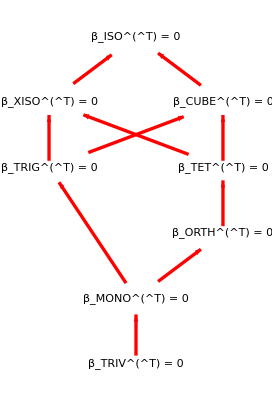

[T] = 1(3 | 0 | 0 | 0 | 0 | 0
0 | 3 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0
0 | 0 | 0 | 0 | 0 | 1)

#### The “defeat” map of TapeTape2021, Section 15.8. (Using the minimization approach of TapeTape2022, its symmetry is identified as monoclinic.)

```mathematica
denominator=160;
TmatDefeat=1/denominator({{252, -12 √6, -52, 16 √6, -24 √2, 0}, {-12 √6, 180, 12 √6, 6, 2 √3, -32}, {-52, 12 √6, 252, 4 √6, -36 √2, 0}, {16 √6, 6, 4 √6, 211, -23 √3, -48}, {-24 √2, 2 √3, -36 √2, -23 √3, 257, -16 √3}, {0, -32, 0, -48, -16 √3, 288}});
```

```mathematica
MatrixNote[TmatDefeat]="Tmat is TmatDefeat";
PrintVoigt[TmatDefeat];
MatrixForm[N[TmatDefeat]]
```

The [T]_𝔹𝔹 matrix is (63/40 | -(3 √(3/2))/20 | -13/40 | (√(3/2))/5 | -3/(10 √2) | 0
-(3 √(3/2))/20 | 9/8 | (3 √(3/2))/20 | 3/80 | (√3)/80 | -1/5
-13/40 | (3 √(3/2))/20 | 63/40 | (√(3/2))/20 | -9/(20 √2) | 0
(√(3/2))/5 | 3/80 | (√(3/2))/20 | 211/160 | -(23 √3)/160 | -3/10
-3/(10 √2) | (√3)/80 | -9/(20 √2) | -(23 √3)/160 | 257/160 | -(√3)/10
0 | -1/5 | 0 | -3/10 | -(√3)/10 | 9/5)

The eigenvalues are: {2,2,2,1,1,1}

The Voigt matrix is (1/240 (401+16 √6) | 5/24-1/(5 √6) | 1/240 (-19+16 √6) | -(3 √(3/2))/20 | 1/240 (-3-8 √6) | -(√(3/2))/10
5/24-1/(5 √6) | 1/60 (83-8 √6) | 5/24-1/(5 √6) | (√(3/2))/20 | 1/120 (3-4 √6) | -(√(3/2))/20
1/240 (-19+16 √6) | 5/24-1/(5 √6) | 1/240 (401+16 √6) | (√(3/2))/10 | 1/240 (-3-8 √6) | (3 √(3/2))/20
-(3 √(3/2))/20 | (√(3/2))/20 | (√(3/2))/10 | 63/80 | -(3 √(3/2))/40 | -13/80
1/240 (-3-8 √6) | 1/120 (3-4 √6) | 1/240 (-3-8 √6) | -(3 √(3/2))/40 | 9/16 | (3 √(3/2))/40
-(√(3/2))/10 | -(√(3/2))/20 | (3 √(3/2))/20 | -13/80 | (3 √(3/2))/40 | 63/80)

11-20-2023 15:51

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = (√(174/5))/5   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.31 = 17.74^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (1.44 | 0. | 0. | 0. | 0. | 0.
0. | 1.44 | 0. | 0. | 0. | 0.
0. | 0. | 1.44 | 0. | 0. | 0.
0. | 0. | 0. | 1.44 | 0. | 0.
0. | 0. | 0. | 0. | 1.44 | 0.
0. | 0. | 0. | 0. | 0. | 1.8)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 3/25 and μ = 18/25, Poisson is 1/14

(1.575 | -0.183712 | -0.325 | 0.244949 | -0.212132 | 0.
-0.183712 | 1.125 | 0.183712 | 0.0375 | 0.0216506 | -0.2
-0.325 | 0.183712 | 1.575 | 0.0612372 | -0.318198 | 0.
0.244949 | 0.0375 | 0.0612372 | 1.31875 | -0.248982 | -0.3
-0.212132 | 0.0216506 | -0.318198 | -0.248982 | 1.60625 | -0.173205
0. | -0.2 | 0. | -0.3 | -0.173205 | 1.8)

```mathematica
cmin=0;cmax=16; dc=2;
contours[TmatDefeat]=Range[cmin,cmax,dc];
MaxForScaling[TmatDefeat]=cmax-dc;
```

```mathematica
tpert[TmatDefeat]=1.89;
```

#### lattice for TmatDefeat:

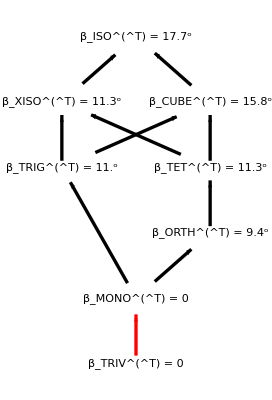

[T] = 1/160(252 | -12 √6 | -52 | 16 √6 | -24 √2 | 0
-12 √6 | 180 | 12 √6 | 6 | 2 √3 | -32
-52 | 12 √6 | 252 | 4 √6 | -36 √2 | 0
16 √6 | 6 | 4 √6 | 211 | -23 √3 | -48
-24 √2 | 2 √3 | -36 √2 | -23 √3 | 257 | -16 √3
0 | -32 | 0 | -48 | -16 √3 | 288)